```mathematica
(*Data*)
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ = 10000000;
Mt = 1000;
Nn = 20;
ranget = 80000;
animationrate = 500;(*dt per second*)



psiQ =τ Cos[α[t]] Cos[γ[t]] ;
alphaQ =τ Sin[γ[t]];

(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rt[t] =l/(Nn+1) ({{Cos[α[t]] Cos[ψ[t]+θ[t]]}, {Cos[α[t]] Sin[ψ[t]+θ[t]]}, {Sin[α[t]]}}); 

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp+Mt)  (Transpose[rm'[t]].rm'[t]);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{γ'[t]+(θ'[t]+ψ'[t])Sin[α[t]]}, {-Cos[γ[t]] α'[t]+Cos[α[t]] Sin[γ[t]] (θ'[t]+ψ'[t])}, {Sin[γ[t]] α'[t]+Cos[α[t]] Cos[γ[t]] (θ'[t]+ψ'[t])}});

ⅈp=({{0.9, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}})  ;
ⅈtether=If[OddQ[Nn],
(*odd number of points, sum of moments of pairs of point masses at ±nδl from centre*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn ((n l)/(Nn+1))^2, 0}, {0, 0, 2 Mt/Nn ((n l)/(Nn+1))^2}}),{n,1,(Nn-1)/2}],
(*even number of points, sum of moments of pairs of point masses at ±(2n-1)/2 δl from centre, (1/2,3/2,5/2...)*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn (((2n-1) l)/(2(Nn+1)))^2, 0}, {0, 0, 2 Mt/Nn (((2n-1) l)/(2(Nn+1)))^2}}),{n,1,Nn/2}]];
Subscript[ⅈ, 123] = ⅈp+ⅈtether;
Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Up1=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Up2=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
Utether=If[OddQ[Nn],
(*sum of potentials for odd number of points (sum from 0 first to get center mass)
position vector is r(centre) + vector in direction from centre to payload, with magnitude length/number of points+1 *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+n*rt[t]].(rm[t]+n*rt[t])))),{n,0,(Nn-1)/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-n*rt[t]].(rm[t]-n*rt[t])))),{n,1,(Nn-1)/2}],
(*sum of potentials for even number of points, same idea but vector is 1/2, 3/2, 5/2 * length/Nn+1 due to symmetry around center *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+(2n-1)/2*rt[t]].(rm[t]+(2n-1)/2*rt[t])))),{n,1,Nn/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-(2n-1)/2*rt[t]].(rm[t]-(2n-1)/2*rt[t])))),{n,1,Nn/2}]];
```

$Aborted

```mathematica
V = Up1+Up2+Utether;
L=T-V;
eqn1=Simplify[D[D[T, ψ'[t]], t]-D[T, ψ[t]]]+ D[V, ψ[t]]-psiQ;
eqn2=Simplify[D[D[T, α'[t]], t]-D[T, α[t]]]+ D[V, α[t]];
eqn3 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn4 =Simplify[D[D[T, rc'[t]], t]-D[T, rc[t]]]+ D[V, rc[t]];
eqn5 = Cos[α[t]] α'[t] (θ'[t]+ψ'[t])+γ''[t]+Sin[α[t]] (θ''[t]+ψ''[t]);
eqn6 =Simplify[D[D[T, γ'[t]], t]-D[T, γ[t]]]+ D[V, γ[t]];
```

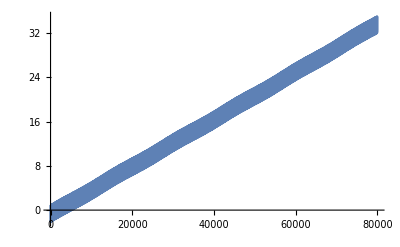

```mathematica
(*initial conditions*)
e=0.3;
alpha0 =0.2;
alphadsh0 = 0.05;
psi0 = 0;
psidsh0 =0;
gamma0=0.9;
r0 = a (1-e);
rdsh0 = 0;
theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;
system=NDSolve[{eqn1[[1]][[1]]==0,eqn2[[1]][[1]]==0,eqn3[[1]][[1]]==0,eqn4[[1]][[1]]==0,eqn6[[1]][[1]]==0,
α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0,γ[0]==gamma0,γ'[0]==0},
{ψ,α,θ,rc,γ},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->10,Method->{"EquationSimplification"->"Residual"}];
gammas[t_]:=γ[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
psis[t_]:=ψ[t]/.system[[1]];
gammadshs[t_]:=Evaluate[γ'[t]/.system[[1]]];
thetadshs[t_]:=Evaluate[θ'[t]/.system[[1]]];
alphadshs[t_]:=Evaluate[α'[t]/.system[[1]]];
psidshs[t_]:=Evaluate[ψ'[t]/.system[[1]]];
Plot[gammas[t],{t,0,ranget}]
```